## Race Prediction and Technique Analysis using FIS-Homologated Data

CloudObject[https://www.wolframcloud.com/obj/ec4af710-70e1-4ad2-9ed5-9f04353143e0]

```mathematica
"https://medias2.fis-ski.com/pdf/homologations/CC/USA/USA_Black_Mountain__Rumford__Maine_18_18-04_5-0.pdf";
```

```mathematica
(*Example graph of a Ski Course from FIS Website, this is required for each event*)
```

#### Processing Homologation Data

```mathematica
(*Fetch graph of homologation*)
pos=ImageValuePositions[-Graphics-, RGBColor[0.12435233160621761, 0.16580310880829016, 0.7098445595854922], .12];
HighlightImage[-Graphics-,{PointSize[Large],pos}]
```

-Graphics-

```mathematica
(*comparison of pixel graph versus graph gives correct units*)

obsLenMax=5500;
obsLenMin=0;
obsHgtMax=310;
obsHgtMin=250;

obsHgtDiff=obsHgtMax-obsHgtMin;
obsLenDiff=obsLenMax-obsLenMin;

lenMax=Max[pos];
lenMin=Min[pos];
hgtMax=Max[Table[pos[[i]][[2]],{i,Length[pos]}]];
hgtMin=Min[Table[pos[[i]][[2]],{i,Length[pos]}]];
hgtDiff=hgtMax-hgtMin;
lenDiff=lenMax-lenMin;

v2Speed10Plus=4.43/4.81;
v1Speed10Plus=4.81/4.43;
v2Speed7Minus=11.53/10.90;
v1Speed7Minus=10.90/11.54;
```

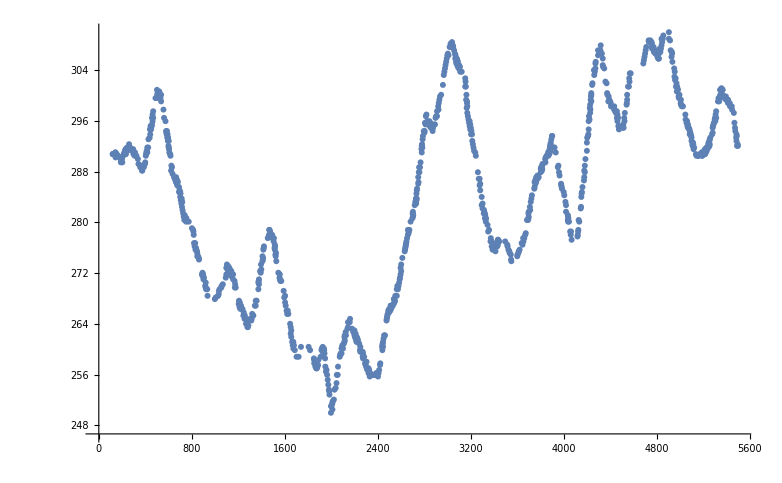

```mathematica
(*apply corrections to pixel graph*)

elevations=Table[{(obsLenDiff/lenDiff)(pos[[i]][[1]]-hgtMin),(obsHgtDiff/hgtDiff)(pos[[i]][[2]]-hgtMin)+obsHgtMin},{i,Length[pos]}];

ListPlot[Table[{(obsLenDiff/lenDiff)(pos[[i]][[1]]-hgtMin),(obsHgtDiff/hgtDiff)(pos[[i]][[2]]-hgtMin)+obsHgtMin},{i,Length[pos]}]]
```

```mathematica
fitFunc=Interpolation[DeleteDuplicatesBy[elevations,First]]
(*create interpolation function to get smooth behav.*)
```

InterpolatingFunction[…]

#### Extrapolate v1/v2 speed ratios at varying inclines using Linear-Regression (done with custom v1 vs. incline efficiency graphs part 2)

```mathematica
(*create efficiency graphs automatically based on data*)

w[x_,n_]:=Round[x,0.01]

p=Predict[{.07->1.05,.10->.92},Method->"LinearRegression"];

compData=MapThread[Rule,{(Range[15]*.01),If[p[#]>1,"v2","v1"]&/@(Range[15]*.01)}]

selector=Classify[compData];
```

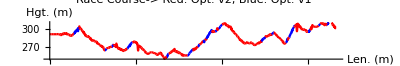

```mathematica
(*Default speed graphs given some pubmed data for xc skiing online*)
kind=Map[selector,Table[Values[elevationSlopeData[[j]]],{j,Length[elevationSlopeData]}]];

diffy=30;

elevationSlopeData=Table[{i,i+30}->w[(fitFunc[i+30]-fitFunc[i])/30,4],{i,1,5000-diffy,diffy}];

slopeData=Table[w[(fitFunc[i+30]-fitFunc[i])/30,4],{i,1,5000-diffy,diffy}];

colorList=Table[{{elevationSlopeData[[i]][[1]][[1]],elevationSlopeData[[i]][[1]][[2]]}->Switch[kind[[i]],"v2",RGBColor[1, 0, 0],"v1",RGBColor[0, 0, 1]]},{i,Length[kind]}];

heightData=Table[fitFunc[elevationSlopeData[[i]][[1]][[1]]],{i,Length[kind]}];

coloredRange=Table[{Keys[colorList[[j]][[1]]][[1]],Keys[colorList[[j]][[1]]][[2]],Values[colorList[[j]]][[1]]},{j,Length[colorList]}];

(*collates graphs*)

Show[Table[Plot[fitFunc[x],{x,Keys[colorList[[j]]][[1]][[1]],Keys[colorList[[j]]][[1]][[2]]},PlotStyle->Values[colorList[[j]]][[1]],PlotRange->{{0,5000},{250,310}}],{j,Length[coloredRange]}],ImageSize->Full,PlotLabel->"Race Course-> Red: Opt. v2, Blue: Opt. v1", AxesLabel->{"Len. (m)","Hgt. (m)"},AspectRatio->1/6]
```

#### Classify race-course sections into “v1” or “v2” based on v1-incline, v2-incline efficiency graphs.

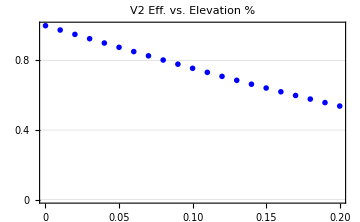
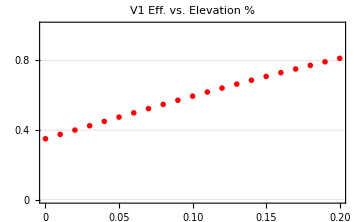

```mathematica
v2SpeedGraph=Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[.25,.1],i/100]/20,"v1"},{i,0,20}];
v1SpeedGraph=Table[i/100->{.35+Tanh[i/40],"v1"},{i,0,20}];

ListPlot[Table[{i/100,1-Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V2 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"],PlotStyle->{Large,Blue}, PlotTheme->"Business",ImageSize->Medium]ListPlot[Table[{i/100,.35+Tanh[i/40]},{i,0,20}],PlotRange->{{0,.2},{0,1}},PlotLabel->Style["V1 Eff. vs. Elevation %",FontSize->12,FontFamily->"Helvetica"], PlotStyle->{Large,Red}, PlotTheme->"Business",ImageSize->Medium]
```

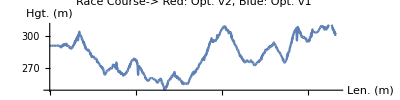

```mathematica
(*Custom speed graphs as a % of maximum speed vs. inclination for v1 and v2*)

bestApproach=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->Values[v2SpeedGraph[[i]]][[2]],Keys[v1SpeedGraph[[i]]]->Values[v1SpeedGraph[[i]]][[2]]],{i,Length[v1SpeedGraph]}];

bestApproachselector=Classify[bestApproach]

kind=Map[bestApproachselector,Table[Values[elevationSlopeData[[j]]],{j,Length[elevationSlopeData]}]]

diffy=30;

elevationSlopeData=Table[{i,i+30}->(fitFunc[i+30]-fitFunc[i])/30,{i,1,5000-diffy,diffy}];

slopeData=Table[(fitFunc[i+30]-fitFunc[i])/30,{i,1,5000-diffy,diffy}];

colorList=Table[{{elevationSlopeData[[i]][[1]][[1]],elevationSlopeData[[i]][[1]][[2]]}->Switch[kind[[i]],"v2",RGBColor[1, 0, 0],"v1",RGBColor[0, 0, 1]]},{i,Length[kind]}];

heightData=Table[fitFunc[elevationSlopeData[[i]][[1]][[1]]],{i,Length[kind]}];

coloredRange=Table[{Keys[colorList[[j]][[1]]][[1]],Keys[colorList[[j]][[1]]][[2]],Values[colorList[[j]]][[1]]},{j,Length[colorList]}];

Show[Table[Plot[fitFunc[x],{x,Keys[colorList[[j]]][[1]][[1]],Keys[colorList[[j]]][[1]][[2]]},PlotStyle->Values[colorList[[j]]][[1]],PlotRange->{{0,5000},{250,310}}],{j,Length[coloredRange]}],PlotLabel->Style["Race Course-> Red: Opt. v2, Blue: Opt. v1",FontSize->18,FontFamily->"Helvetica"], AxesLabel->{"Len. (m)","Hgt. (m)"},ImageSize->Full,AspectRatio->1/4]
```

#### Calculate time on course given v1-v2/slope efficiency graphs

```mathematica
(*calulate time on course*)
v1SpeedGraph=Table[i/100->{.35+Tanh[i/40],"v1"},{i,0,20}];
v2SpeedGraph=Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[.25,.1],i/100]/20,"v1"},{i,0,20}];
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

maxSpeed=4.47(*meters/sec*);

diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

Print["Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60"]

Total[Table[Take[distanceTables,166][[i]]/bestPart[[i]][[1]]*(1/maxSpeed),{i,Length[bestPart]}]]/60
```

Minutes on Race Course ~ Sum* Delta_Distance * 1/Eff. * 1/Max Speed ~ Sum* Delta_Distance * speed. Div 60

17.2831

#### Perturb efficiency graphs with variable gaussian function to determine efficiency/incline weakness.

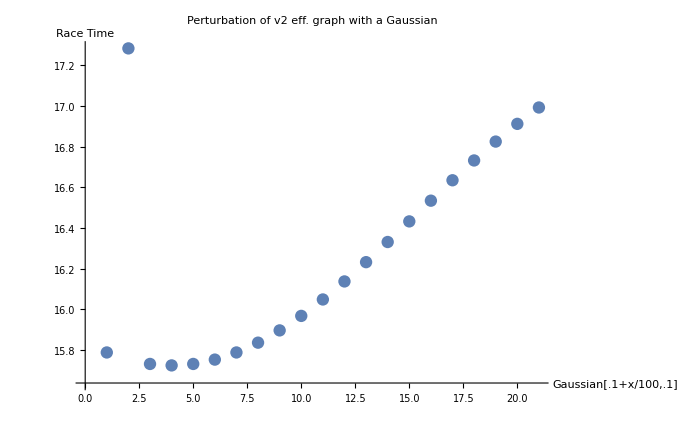

therefore, this v2 eff. graph could greatly improve performance if it were increased ~5/20 ~25% capacity~5% slope. therefore, v2 training at medium elevation is optimal

```mathematica
speedGraphsForV2=Table[Table[i/100->{1-Tanh[i/40]+PDF[NormalDistribution[j/100,.1],i/100]/20,"v2"},{i,0,20}],{j,0,20}];
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

perturbationGaussianV2Eff={#,getSpeedAdjustment[speedGraphsForV2[[#]],fitFunc,v1SpeedGraph,elevationSlopeData]}&/@Range[Length[speedGraphsForV2]];

ListPlot[perturbationGaussianV2Eff,PlotLabel->"Perturbation of v2 eff. graph with a Gaussian",AxesLabel->{"Gaussian[.1+x/100,.1]" ,"Race Time"}]

Print["therefore, this v2 eff. graph could greatly improve performance if it were increased ~5/20 ~25% capacity~5% slope. therefore, v2 training at medium elevation is optimal"]

getSpeedAdjustment[v2SpeedGraph,fitFunc,v1SpeedGraph,elevationSlopeData]:=Module[{},

maxSpeed=4.47(*meters/sec*);

diffy=30;

distanceTables=Table[Sqrt[((fitFunc[i+diffy]-fitFunc[i])^2+diffy^2)],{i,1,5000,diffy}];

slopeTable=Table[Values[elevationSlopeData[[i]]],{i,Length[elevationSlopeData]}];

Total[Table[distanceTables[[i]],{i,Length[distanceTables]}]];

bestApproachEff=Table[If[Values[v2SpeedGraph[[i]]][[1]]>Values[v1SpeedGraph[[i]]][[1]],Keys[v2SpeedGraph[[i]]]->{Values[v2SpeedGraph[[i]]][[1]],Values[v2SpeedGraph[[i]]][[2]]},Keys[v1SpeedGraph[[i]]]->{Values[v1SpeedGraph[[i]]][[1]],Values[v1SpeedGraph[[i]]][[2]]}],{i,Length[v1SpeedGraph]}];

bestPart=Table[Last[Switch[Select[bestApproachEff,slopeTable[[i]]>Keys[#1]&],{},0->{1.25,"v2-alt"},Except[_Empty],Last[Select[bestApproachEff,slopeTable[[8]]>Keys[#1]&]]]],{i,Length[slopeTable]}];

Total[Table[Take[distanceTables,166][[i]]/bestPart[[i]][[1]]*(1/maxSpeed),{i,Length[bestPart]}]]/60

]
```

```mathematica
speedGraphsForV1=Table[Table[i/100->{Tanh[i/40]+PDF[NormalDistribution[j/100,.1],i/100]/20,"v2"},{i,0,20}],{j,0,5}]
(*v2SpeedGraph=Table[g[i/100,3]->{g[1-Tanh[i/40],3],"v2"},{i,0,20}]*)

perturbationGaussianV1Eff={#,getSpeedAdjustment[speedGraphsForV1[[#]],fitFunc,v2SpeedGraph,elevationSlopeData]}&/@Range[Length[speedGraphsForV1]]

ListPlot[perturbationGaussianV1Eff,PlotLabel->"Perturbation of v2 eff. graph with a Gaussian",AxesLabel->{"Gaussian[.1+x/100,.1]" ,"Race Time"}]
```

```mathematica
Table[s[[1]][[i]],{i,10}]//TableForm
```

```mathematica
Off[InterpolatingFunction::dmval]
Off[General::stop]
Off[Classify::mincnb]
```